```mathematica
(*Mathematica*)
```

```mathematica
CompanionMatrix[p_, x_] := Module[{cl=CoefficientList[p, x], deg, m}, cl=Drop[cl/Last[cl], -1]; deg=Length[cl]; If[deg==1, {-cl}, m=RotateLeft[IdentityMatrix[deg]]; m[[ -1]]=-cl; Transpose[m]]];
```

```mathematica
(*Weeks hyperbolic 3 manifold minimal Polynomial generalized*)
```

```mathematica
p[x_,n_]=x^(3*n)-x^(2*n)+1
```

1-x^(2 n)+x^(3 n)

```mathematica
mp=-1/x/.NSolve[p[x,1]==0][[1]]
```

1.32472

```mathematica
Table[p[x,i],{i,1,10}]
```

{1-x^2+x^3,1-x^4+x^6,1-x^6+x^9,1-x^8+x^12,1-x^10+x^15,1-x^12+x^18,1-x^14+x^21,1-x^16+x^24,1-x^18+x^27,1-x^20+x^30}

```mathematica
(*Weeks manifold volume calculation using PolyLog: L-systen volume*)
```

```mathematica
N[Roots[z^3-z^2+1==0,z][[3,2]],30]
```

0.877438833123346380024754448179+0.7448617666197442365931704286 ⅈ

```mathematica
z0=z/.NSolve[z^3-z^2+1==0,z,30][[2]]
```

0.877438833123346380024754448179-0.7448617666197442365931704286 ⅈ

```mathematica
vw30=Im[PolyLog[2,z0]+Log[Abs[z0]] Log[1-z0]]
```

-0.9427073627769277209212996031

```mathematica
(*book volume*)
```

```mathematica
vw=0.94270736277692772092
```

0.9427073627769277209

```mathematica
p[x,5]
```

1-x^10+x^15

```mathematica
1-x^10+x^15
```

1-x^10+x^15

```mathematica
(*n=5 as D_6 close packing of spheres: minimal root of the polynomial*)
```

```mathematica
root=x/.NSolve[p[x,5]==0,30][[1]]
```

-0.945312314206677076255923550054

```mathematica
(* comparing the two results: the root minimal Eigenvalue gives a slightly larger volume*)
```

```mathematica
root/vw30
```

1.002763266239987735655862531

```mathematica
(*quantum scale residues to four power levels of alpha*)
```

```mathematica
α=1/137.035999206;
```

```mathematica
((((1.0027632662399877356558625311563506375913761343733626266743-1)/(3*α/8)-1)/(mp*α)-1)/(Pi*α/2)-1)/α-1
```

-0.0213519

```mathematica
Abs[{-0.945312314206677,-0.9086808024297136-0.4818201395510902 ⅈ,-0.9086808024297136+0.4818201395510902 ⅈ,-0.7390359938153501-0.7153161870296925 ⅈ,-0.7390359938153501+0.7153161870296925 ⅈ,-0.29211757008177325-0.8990454363603119 ⅈ,-0.29211757008177325+0.8990454363603119 ⅈ,0.1774403729892591-1.0130974097364838 ⅈ,0.1774403729892591+1.0130974097364838 ⅈ,0.4519314393422701-0.9239098558384168 ⅈ,0.4519314393422701+0.9239098558384168 ⅈ,0.7647737271851118-0.5556406371011533 ⅈ,0.7647737271851118+0.5556406371011533 ⅈ,1.0183449839135343-0.14430849358053538 ⅈ,1.0183449839135343+0.14430849358053538 ⅈ}]
```

{0.945312,1.02852,1.02852,1.02852,1.02852,0.945312,0.945312,1.02852,1.02852,1.02852,1.02852,0.945312,0.945312,1.02852,1.02852}

```mathematica
(*5 at 0.945312314206677 low energy:10 at higher energy 1.0285190555266053*)
```

```mathematica
Union[{0.945312314206677,1.0285190555266053,1.0285190555266053,1.0285190555266053,1.0285190555266053,0.945312314206677,0.945312314206677,1.0285190555266053,1.0285190555266053,1.0285190555266053,1.0285190555266053,0.945312314206677,0.945312314206677,1.0285190555266053,1.0285190555266053}]
```

{0.945312,1.02852}

```mathematica
(* transition quantum energy/ volume between lower and upper states*)
-(0.945312314206677-1.0285190555266053)
```

0.0832067

```mathematica
Union[Abs[{-0.945312314206677,-0.9086808024297136-0.4818201395510902 ⅈ,-0.9086808024297136+0.4818201395510902 ⅈ,-0.7390359938153501-0.7153161870296925 ⅈ,-0.7390359938153501+0.7153161870296925 ⅈ,-0.29211757008177325-0.8990454363603119 ⅈ,-0.29211757008177325+0.8990454363603119 ⅈ,0.1774403729892591-1.0130974097364838 ⅈ,0.1774403729892591+1.0130974097364838 ⅈ,0.4519314393422701-0.9239098558384168 ⅈ,0.4519314393422701+0.9239098558384168 ⅈ,0.7647737271851118-0.5556406371011533 ⅈ,0.7647737271851118+0.5556406371011533 ⅈ,1.0183449839135343-0.14430849358053538 ⅈ,1.0183449839135343+0.14430849358053538 ⅈ}/0.08320674131992822//Chop]]
```

```mathematica
{11.36100632245614,11.361006322456142,12.36100632245614}
```

```mathematica
Apply[Plus,Abs[{-0.945312314206677,-0.9086808024297136-0.4818201395510902 ⅈ,-0.9086808024297136+0.4818201395510902 ⅈ,-0.7390359938153501-0.7153161870296925 ⅈ,-0.7390359938153501+0.7153161870296925 ⅈ,-0.29211757008177325-0.8990454363603119 ⅈ,-0.29211757008177325+0.8990454363603119 ⅈ,0.1774403729892591-1.0130974097364838 ⅈ,0.1774403729892591+1.0130974097364838 ⅈ,0.4519314393422701-0.9239098558384168 ⅈ,0.4519314393422701+0.9239098558384168 ⅈ,0.7647737271851118-0.5556406371011533 ⅈ,0.7647737271851118+0.5556406371011533 ⅈ,1.0183449839135343-0.14430849358053538 ⅈ,1.0183449839135343+0.14430849358053538 ⅈ}/0.08320674131992822//Chop]]
```

180.415

```mathematica
Table[x/.NSolve[p[x,i]==0,x],{i,1,10}]
```

{{-0.754878,0.877439-0.744862 ⅈ,0.877439+0.744862 ⅈ},{-1.00708-0.369814 ⅈ,-1.00708+0.369814 ⅈ,0.-0.868837 ⅈ,0.+0.868837 ⅈ,1.00708-0.369814 ⅈ,1.00708+0.369814 ⅈ},{-0.910526,-0.720623-0.760901 ⅈ,-0.720623+0.760901 ⅈ,-0.298648-1.00453 ⅈ,-0.298648+1.00453 ⅈ,0.455263-0.788538 ⅈ,0.455263+0.788538 ⅈ,1.01927-0.243627 ⅈ,1.01927+0.243627 ⅈ},{-1.01978-0.18132 ⅈ,-1.01978+0.18132 ⅈ,-0.659104-0.659104 ⅈ,-0.659104+0.659104 ⅈ,-0.18132-1.01978 ⅈ,-0.18132+1.01978 ⅈ,0.18132-1.01978 ⅈ,0.18132+1.01978 ⅈ,0.659104-0.659104 ⅈ,0.659104+0.659104 ⅈ,1.01978-0.18132 ⅈ,1.01978+0.18132 ⅈ},{-0.945312,-0.908681-0.48182 ⅈ,-0.908681+0.48182 ⅈ,-0.739036-0.715316 ⅈ,-0.739036+0.715316 ⅈ,-0.292118-0.899045 ⅈ,-0.292118+0.899045 ⅈ,0.17744-1.0131 ⅈ,0.17744+1.0131 ⅈ,0.451931-0.92391 ⅈ,0.451931+0.92391 ⅈ,0.764774-0.555641 ⅈ,0.764774+0.555641 ⅈ,1.01834-0.144308 ⅈ,1.01834+0.144308 ⅈ},{-1.01667-0.119816 ⅈ,-1.01667+0.119816 ⅈ,-0.826374-0.477107 ⅈ,-0.826374+0.477107 ⅈ,-0.612101-0.820558 ⅈ,-0.612101+0.820558 ⅈ,-0.404574-0.940374 ⅈ,-0.404574+0.940374 ⅈ,0.-0.954215 ⅈ,0.+0.954215 ⅈ,0.404574-0.940374 ⅈ,0.404574+0.940374 ⅈ,0.612101-0.820558 ⅈ,0.612101+0.820558 ⅈ,0.826374-0.477107 ⅈ,0.826374+0.477107 ⅈ,1.01667-0.119816 ⅈ,1.01667+0.119816 ⅈ},{-0.960625,-0.959043-0.348175 ⅈ,-0.959043+0.348175 ⅈ,-0.870168-0.532726 ⅈ,-0.870168+0.532726 ⅈ,-0.59894-0.751047 ⅈ,-0.59894+0.751047 ⅈ,-0.325739-0.966893 ⅈ,-0.325739+0.966893 ⅈ,-0.126038-1.01247 ⅈ,-0.126038+1.01247 ⅈ,0.213759-0.93654 ⅈ,0.213759+0.93654 ⅈ,0.552853-0.857522 ⅈ,0.552853+0.857522 ⅈ,0.713-0.729808 ⅈ,0.713+0.729808 ⅈ,0.865493-0.416799 ⅈ,0.865493+0.416799 ⅈ,1.01514-0.102418 ⅈ,1.01514+0.102418 ⅈ},{-1.01379-0.0894267 ⅈ,-1.01379+0.0894267 ⅈ,-0.891969-0.369466 ⅈ,-0.891969+0.369466 ⅈ,-0.780095-0.653626 ⅈ,-0.780095+0.653626 ⅈ,-0.653626-0.780095 ⅈ,-0.653626+0.780095 ⅈ,-0.369466-0.891969 ⅈ,-0.369466+0.891969 ⅈ,-0.0894267-1.01379 ⅈ,-0.0894267+1.01379 ⅈ,0.0894267-1.01379 ⅈ,0.0894267+1.01379 ⅈ,0.369466-0.891969 ⅈ,0.369466+0.891969 ⅈ,0.653626-0.780095 ⅈ,0.653626+0.780095 ⅈ,0.780095-0.653626 ⅈ,0.780095+0.653626 ⅈ,0.891969-0.369466 ⅈ,0.891969+0.369466 ⅈ,1.01379-0.0894267 ⅈ,1.01379+0.0894267 ⅈ},{-0.978712-0.271772 ⅈ,-0.978712+0.271772 ⅈ,-0.969239,-0.924429-0.420914 ⅈ,-0.924429+0.420914 ⅈ,-0.74248-0.623015 ⅈ,-0.74248+0.623015 ⅈ,-0.575045-0.837294 ⅈ,-0.575045+0.837294 ⅈ,-0.437595-0.916651 ⅈ,-0.437595+0.916651 ⅈ,-0.168307-0.954514 ⅈ,-0.168307+0.954514 ⅈ,0.0976919-1.01104 ⅈ,0.0976919+1.01104 ⅈ,0.253994-0.983476 ⅈ,0.253994+0.983476 ⅈ,0.484619-0.839385 ⅈ,0.484619+0.839385 ⅈ,0.724718-0.711703 ⅈ,0.724718+0.711703 ⅈ,0.826737-0.590122 ⅈ,0.826737+0.590122 ⅈ,0.910786-0.331499 ⅈ,0.910786+0.331499 ⅈ,1.01264-0.0793568 ⅈ,1.01264+0.0793568 ⅈ},{-1.01165-0.0713235 ⅈ,-1.01165+0.0713235 ⅈ,-0.924685-0.300448 ⅈ,-0.924685+0.300448 ⅈ,-0.860363-0.53693 ⅈ,-0.860363+0.53693 ⅈ,-0.776518-0.652334 ⅈ,-0.776518+0.652334 ⅈ,-0.571487-0.786584 ⅈ,-0.571487+0.786584 ⅈ,-0.380449-0.940094 ⅈ,-0.380449+0.940094 ⅈ,-0.244784-0.984175 ⅈ,-0.244784+0.984175 ⅈ,0.-0.972272 ⅈ,0.+0.972272 ⅈ,0.244784-0.984175 ⅈ,0.244784+0.984175 ⅈ,0.380449-0.940094 ⅈ,0.380449+0.940094 ⅈ,0.571487-0.786584 ⅈ,0.571487+0.786584 ⅈ,0.776518-0.652334 ⅈ,0.776518+0.652334 ⅈ,0.860363-0.53693 ⅈ,0.860363+0.53693 ⅈ,0.924685-0.300448 ⅈ,0.924685+0.300448 ⅈ,1.01165-0.0713235 ⅈ,1.01165+0.0713235 ⅈ}}

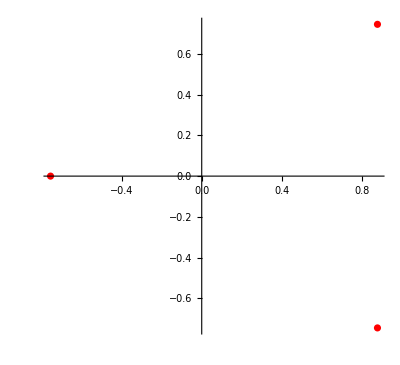
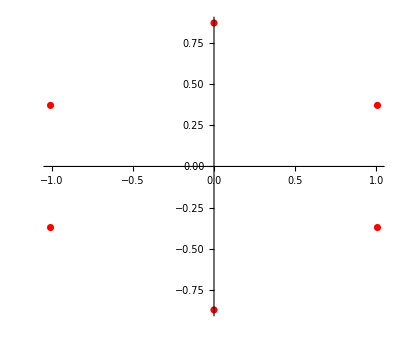
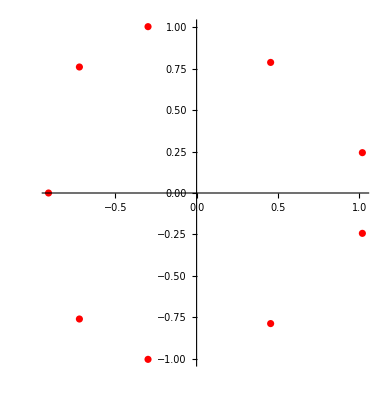
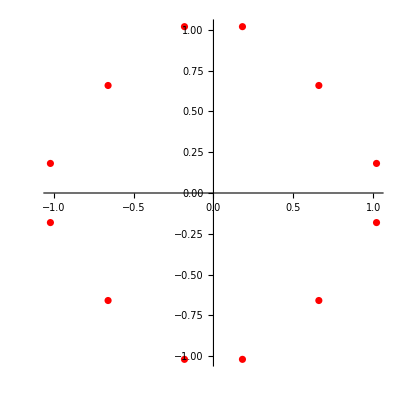
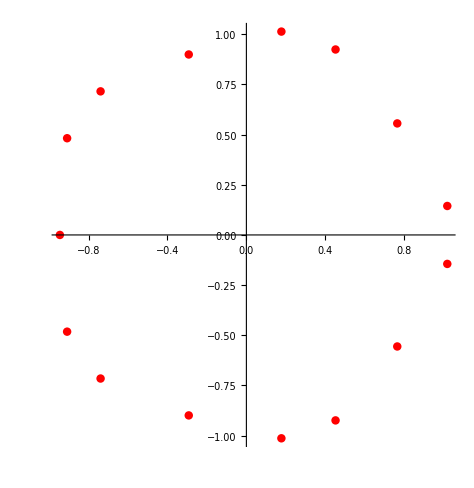
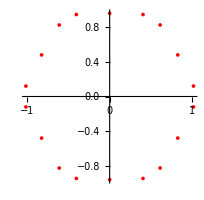
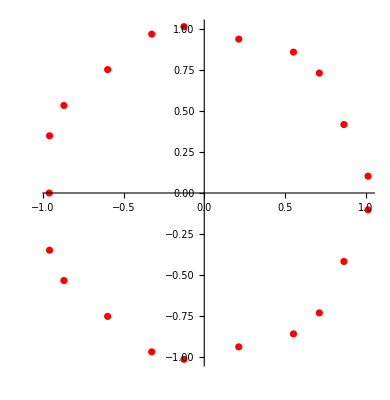
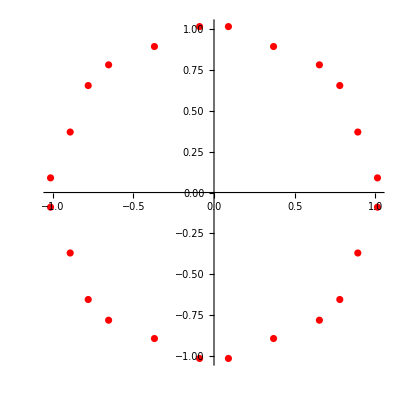

```mathematica
Table[ComplexListPlot[x/.NSolve[p[x,i]==0,x],PlotRange->All,PlotStyle->Red],{i,1,10}]
```

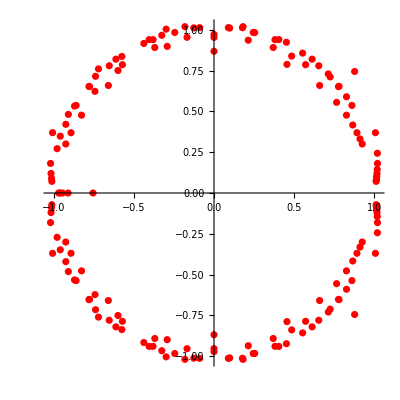

```mathematica
Show[%,PlotRange->All,ImageSize->Full]
```

```mathematica
v=Table[Transpose[CompanionMatrix[p[x,i],x]],{i,10}]
```

{{{0,1,0},{0,0,1},{-1,0,1}},{{0,1,0,0,0,0},{0,0,1,0,0,0},{0,0,0,1,0,0},{0,0,0,0,1,0},{0,0,0,0,0,1},{-1,0,0,0,1,0}},{{0,1,0,0,0,0,0,0,0},{0,0,1,0,0,0,0,0,0},{0,0,0,1,0,0,0,0,0},{0,0,0,0,1,0,0,0,0},{0,0,0,0,0,1,0,0,0},{0,0,0,0,0,0,1,0,0},{0,0,0,0,0,0,0,1,0},{0,0,0,0,0,0,0,0,1},{-1,0,0,0,0,0,1,0,0}},{{0,1,0,0,0,0,0,0,0,0,0,0},{0,0,1,0,0,0,0,0,0,0,0,0},{0,0,0,1,0,0,0,0,0,0,0,0},{0,0,0,0,1,0,0,0,0,0,0,0},{0,0,0,0,0,1,0,0,0,0,0,0},{0,0,0,0,0,0,1,0,0,0,0,0},{0,0,0,0,0,0,0,1,0,0,0,0},{0,0,0,0,0,0,0,0,1,0,0,0},{0,0,0,0,0,0,0,0,0,1,0,0},{0,0,0,0,0,0,0,0,0,0,1,0},{0,0,0,0,0,0,0,0,0,0,0,1},{-1,0,0,0,0,0,0,0,1,0,0,0}},{{0,1,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,1,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,1,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,1,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,1,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,1,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,1,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,1,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,1,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,1,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,1,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,1,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,1,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,1},{-1,0,0,0,0,0,0,0,0,0,1,0,0,0,0}},{{0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1},{-1,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0}},{{0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1},{-1,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0}},{{0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1},{-1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0}},{{0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1},{-1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0}},{{0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1},{-1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0}}}

```mathematica
Table[N[Eigenvalues[v[[i]]]]//Chop,{i,Length[v]}]
```

{{0.877439+0.744862 ⅈ,0.877439-0.744862 ⅈ,-0.754878},{-1.00708+0.369814 ⅈ,-1.00708-0.369814 ⅈ,1.00708+0.369814 ⅈ,1.00708-0.369814 ⅈ,0.+0.868837 ⅈ,0.-0.868837 ⅈ},{1.01927+0.243627 ⅈ,1.01927-0.243627 ⅈ,-0.298648-1.00453 ⅈ,-0.720623-0.760901 ⅈ,-0.298648+1.00453 ⅈ,-0.720623+0.760901 ⅈ,-0.910526,0.455263+0.788538 ⅈ,0.455263-0.788538 ⅈ},{-1.01978+0.18132 ⅈ,-1.01978-0.18132 ⅈ,-0.18132+1.01978 ⅈ,-0.18132-1.01978 ⅈ,0.18132+1.01978 ⅈ,0.18132-1.01978 ⅈ,1.01978+0.18132 ⅈ,1.01978-0.18132 ⅈ,-0.659104+0.659104 ⅈ,-0.659104-0.659104 ⅈ,0.659104+0.659104 ⅈ,0.659104-0.659104 ⅈ},{-0.908681-0.48182 ⅈ,-0.739036-0.715316 ⅈ,1.01834+0.144308 ⅈ,1.01834-0.144308 ⅈ,0.451931+0.92391 ⅈ,0.451931-0.92391 ⅈ,-0.908681+0.48182 ⅈ,-0.739036+0.715316 ⅈ,0.17744+1.0131 ⅈ,0.17744-1.0131 ⅈ,-0.292118+0.899045 ⅈ,-0.292118-0.899045 ⅈ,0.764774-0.555641 ⅈ,-0.945312,0.764774+0.555641 ⅈ},{-1.01667+0.119816 ⅈ,-1.01667-0.119816 ⅈ,1.01667+0.119816 ⅈ,1.01667-0.119816 ⅈ,-0.404574-0.940374 ⅈ,0.404574+0.940374 ⅈ,-0.612101-0.820558 ⅈ,0.612101+0.820558 ⅈ,-0.404574+0.940374 ⅈ,0.404574-0.940374 ⅈ,-0.612101+0.820558 ⅈ,0.612101-0.820558 ⅈ,-0.826374-0.477107 ⅈ,0.826374+0.477107 ⅈ,0.+0.954215 ⅈ,0.-0.954215 ⅈ,-0.826374+0.477107 ⅈ,0.826374-0.477107 ⅈ},{-0.870168-0.532726 ⅈ,-0.959043-0.348175 ⅈ,1.01514+0.102418 ⅈ,1.01514-0.102418 ⅈ,0.552853+0.857522 ⅈ,0.713+0.729808 ⅈ,-0.126038-1.01247 ⅈ,-0.325739-0.966893 ⅈ,-0.325739+0.966893 ⅈ,-0.126038+1.01247 ⅈ,0.713-0.729808 ⅈ,0.552853-0.857522 ⅈ,-0.870168+0.532726 ⅈ,-0.959043+0.348175 ⅈ,-0.960625,-0.59894-0.751047 ⅈ,0.213759+0.93654 ⅈ,0.213759-0.93654 ⅈ,-0.59894+0.751047 ⅈ,0.865493-0.416799 ⅈ,0.865493+0.416799 ⅈ},{-1.01379+0.0894267 ⅈ,-1.01379-0.0894267 ⅈ,-0.0894267+1.01379 ⅈ,-0.0894267-1.01379 ⅈ,0.0894267+1.01379 ⅈ,0.0894267-1.01379 ⅈ,1.01379+0.0894267 ⅈ,1.01379-0.0894267 ⅈ,-0.780095-0.653626 ⅈ,0.780095+0.653626 ⅈ,-0.653626-0.780095 ⅈ,0.653626+0.780095 ⅈ,-0.780095+0.653626 ⅈ,-0.653626+0.780095 ⅈ,0.653626-0.780095 ⅈ,0.780095-0.653626 ⅈ,-0.891969-0.369466 ⅈ,-0.369466+0.891969 ⅈ,0.369466-0.891969 ⅈ,0.891969+0.369466 ⅈ,-0.369466-0.891969 ⅈ,0.369466+0.891969 ⅈ,-0.891969+0.369466 ⅈ,0.891969-0.369466 ⅈ},{0.724718-0.711703 ⅈ,1.01264+0.0793568 ⅈ,-0.924429-0.420914 ⅈ,1.01264-0.0793568 ⅈ,0.0976919+1.01104 ⅈ,-0.978712+0.271772 ⅈ,-0.924429+0.420914 ⅈ,0.826737+0.590122 ⅈ,0.826737-0.590122 ⅈ,0.724718+0.711703 ⅈ,0.0976919-1.01104 ⅈ,-0.978712-0.271772 ⅈ,0.253994+0.983476 ⅈ,0.253994-0.983476 ⅈ,-0.437595-0.916651 ⅈ,-0.575045-0.837294 ⅈ,-0.575045+0.837294 ⅈ,-0.437595+0.916651 ⅈ,0.910786+0.331499 ⅈ,0.910786-0.331499 ⅈ,-0.74248+0.623015 ⅈ,-0.74248-0.623015 ⅈ,-0.969239,-0.168307+0.954514 ⅈ,-0.168307-0.954514 ⅈ,0.484619+0.839385 ⅈ,0.484619-0.839385 ⅈ},{-1.01165+0.0713235 ⅈ,-1.01165-0.0713235 ⅈ,-0.776518-0.652334 ⅈ,0.776518+0.652334 ⅈ,-0.860363+0.53693 ⅈ,0.860363-0.53693 ⅈ,1.01165+0.0713235 ⅈ,1.01165-0.0713235 ⅈ,-0.860363-0.53693 ⅈ,0.860363+0.53693 ⅈ,-0.244784+0.984175 ⅈ,-0.244784-0.984175 ⅈ,0.244784+0.984175 ⅈ,0.244784-0.984175 ⅈ,-0.380449+0.940094 ⅈ,-0.380449-0.940094 ⅈ,0.380449+0.940094 ⅈ,0.380449-0.940094 ⅈ,-0.776518+0.652334 ⅈ,0.776518-0.652334 ⅈ,-0.571487-0.786584 ⅈ,0.571487+0.786584 ⅈ,-0.924685-0.300448 ⅈ,0.924685+0.300448 ⅈ,-0.571487+0.786584 ⅈ,0.571487-0.786584 ⅈ,0.+0.972272 ⅈ,0.-0.972272 ⅈ,-0.924685+0.300448 ⅈ,0.924685-0.300448 ⅈ}}

```mathematica
Max[Abs[N[Eigenvalues[v[[5]]]]]]
```

```mathematica
1.0285190555266055
```

```mathematica
(*a new interpretation of the Weeks hyperbolic 3 manifold volume as being determined by the minimal Eigenvalue energy of
the D_6 15 vertices unit cell of the close packing of spheres at an order 15 generalized minimal polynomial *)
```

```mathematica
Min[Abs[N[Eigenvalues[v[[5]]]]]]
```

```mathematica
0.945312314206677
```

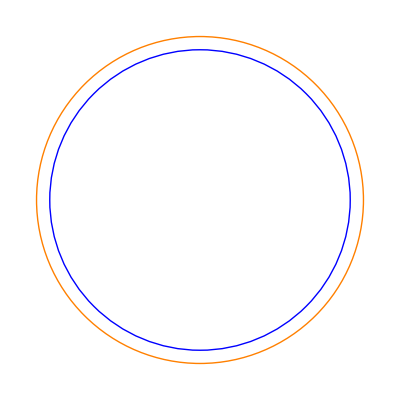

```mathematica
ga=Graphics[{Blue,Circle[{0,0},0.945312314206677],Orange,Circle[{0,0},1.0285190555266055]}]
```

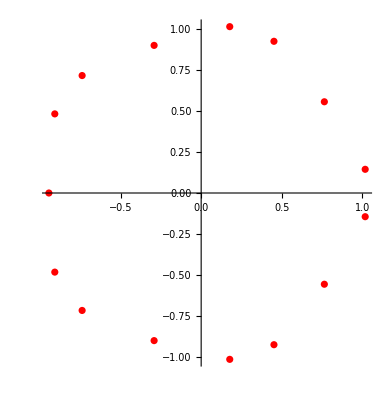

```mathematica
gb=ComplexListPlot[N[Eigenvalues[v[[5]]]],PlotStyle->Red,ImageSize->Full]
```

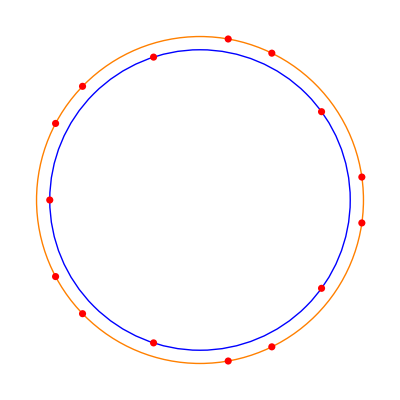

```mathematica
Show[{ga,gb}]
```

```mathematica
(*D_5d unit cell model of Weeks hyperbolic 3 manifold energy as close packing of spheres*)
```

```mathematica
(*5 inner spheres 10 outer spheres  by Eigenvalue energy scaling*)
```

```mathematica
g1=N[Table[1.0285190555266055*{Cos[2*Pi*i/5],Sin[2*Pi*i/5],1},{i,5}]]
```

{{0.31783,0.97818,1.02852},{-0.832089,0.604548,1.02852},{-0.832089,-0.604548,1.02852},{0.31783,-0.97818,1.02852},{1.02852,0.,1.02852}}

```mathematica
g2=N[Table[0.945312314206677*{Cos[2*Pi*i/5+2*Pi/10],Sin[2*Pi*i/5+2*Pi/10],0},{i,5}]]
```

{{-0.292118,0.899045,0.},{-0.945312,0.,0.},{-0.292118,-0.899045,0.},{0.764774,-0.555641,0.},{0.764774,0.555641,0.}}

```mathematica
g3=N[Table[1.0285190555266055*{Cos[2*Pi*i/5],Sin[2*Pi*i/5],-1},{i,5}]]
```

{{0.31783,0.97818,-1.02852},{-0.832089,0.604548,-1.02852},{-0.832089,-0.604548,-1.02852},{0.31783,-0.97818,-1.02852},{1.02852,0.,-1.02852}}

```mathematica
ListPointPlot3D[{g1,g2,g3},PlotStyle->{Blue,Red,Blue},ImageSize->Full]
```

-Graphics3D-

```mathematica
(*D_5d  Menger cube by Roger Bagula 26 Oct 2025©*)
(* symmetric isomer of the Menger cube*)
(* patterned from Menger cube code by Szabolcs Horvát <szhorvat@gmail.com>,University of Bergen in Mathematica newsgroup: Mon,28 May 2007 09:10:50*)
```

```mathematica
pieces=Join[g1,g2,g3]
```

{{0.31783,0.97818,1.02852},{-0.832089,0.604548,1.02852},{-0.832089,-0.604548,1.02852},{0.31783,-0.97818,1.02852},{1.02852,0.,1.02852},{-0.292118,0.899045,0.},{-0.945312,0.,0.},{-0.292118,-0.899045,0.},{0.764774,-0.555641,0.},{0.764774,0.555641,0.},{0.31783,0.97818,-1.02852},{-0.832089,0.604548,-1.02852},{-0.832089,-0.604548,-1.02852},{0.31783,-0.97818,-1.02852},{1.02852,0.,-1.02852}}

```mathematica
Length[pieces]
```

15

```mathematica
(*Moran Dimension of Menger cube fractal*)
```

```mathematica
N[Log[Length[pieces]]/Log[3]]
```

2.46497

```mathematica
menger1[cornerPt_, sideLen_, n_] :=
  menger1[cornerPt + #1*(sideLen/3), sideLen/3, n - 1] & /@ pieces;
 menger1[cornerPt_, sideLen_, 0] :=
  {ColorData["Rainbow"][N[Apply[Plus,cornerPt]]],EdgeForm[],Cuboid[cornerPt, cornerPt + sideLen*{1, 1, 1}]};
```

```mathematica
gr=Show[Graphics3D[Flatten[menger1[{0, 0, 0}, 1, 4]]],Boxed->False,ImageSize->2000,Background->Black,ViewPoint->{2,2,2}];
```

```mathematica
Export["D_5d_Menger_cube_ratio3_Level4_scaled_Rainbow.jpg" ,gr]
```

D_5d_Menger_cube_ratio3_Level4_scaled_Rainbow.jpg

```mathematica
g3=Show[gr,PlotRange->All,ViewPoint->{0, -2, 2},ImageSize->{2000,2000}];
```

```mathematica
g4=Show[gr,PlotRange->All,ViewPoint->Above,ImageSize->{2000,2000}];
```

```mathematica
g5=Show[gr,PlotRange->All,ViewPoint->{1.3, -2, 3},ImageSize->{2000,2000}];
```

```mathematica
Export["D_5d_MengerCube_ratio3_Level4_Rainbow_scaled_grid.jpg",GraphicsGrid[{{gr,g3},{g4,g5}},ImageSize->4000]]
```

D_5d_MengerCube_ratio3_Level4_Rainbow_scaled_grid.jpg

```mathematica
(*end*)
```

```mathematica
(* Mathematica*)
<<ComputationalGeometry`
```

```mathematica
pts={{0.31782986719619133,0.978179749892315,1.0285190555266055},{-0.8320893949594941,0.604548332540322,1.0285190555266055},{-0.8320893949594941,-0.604548332540322,1.0285190555266055},{0.31782986719619133,-0.978179749892315,1.0285190555266055},{1.0285190555266055,0.,1.0285190555266055},{-0.2921175700817733,0.8990454363603119,0.},{-0.945312314206677,0.,0.},{-0.2921175700817733,-0.8990454363603119,0.},{0.7647737271851118,-0.5556406371011533,0.},{0.7647737271851118,0.5556406371011533,0.},{0.31782986719619133,0.978179749892315,-1.0285190555266055},{-0.8320893949594941,0.604548332540322,-1.0285190555266055},{-0.8320893949594941,-0.604548332540322,-1.0285190555266055},{0.31782986719619133,-0.978179749892315,-1.0285190555266055},{1.0285190555266055,0.,-1.0285190555266055}}
```

{{0.31783,0.97818,1.02852},{-0.832089,0.604548,1.02852},{-0.832089,-0.604548,1.02852},{0.31783,-0.97818,1.02852},{1.02852,0.,1.02852},{-0.292118,0.899045,0.},{-0.945312,0.,0.},{-0.292118,-0.899045,0.},{0.764774,-0.555641,0.},{0.764774,0.555641,0.},{0.31783,0.97818,-1.02852},{-0.832089,0.604548,-1.02852},{-0.832089,-0.604548,-1.02852},{0.31783,-0.97818,-1.02852},{1.02852,0.,-1.02852}}

```mathematica
ptsn=Table[Hue[Norm[pts[[i]]]/1.75],{i,Length[pts]}]
```

{Hue[0.8311689128485096],Hue[0.8311689128485097],Hue[0.8311689128485097],Hue[0.8311689128485096],Hue[0.8311689128485097],Hue[0.5401784652609583],Hue[0.5401784652609583],Hue[0.5401784652609583],Hue[0.5401784652609583],Hue[0.5401784652609583],Hue[0.8311689128485096],Hue[0.8311689128485097],Hue[0.8311689128485097],Hue[0.8311689128485096],Hue[0.8311689128485097]}

```mathematica
(* Voronoi diagram*)
```

```mathematica
a=Union[Most/@pts];
```

```mathematica
g1=Show[{
DiagramPlot[a],
Graphics[{Red,PointSize[.005],Point[a]}]
},PlotRange->All,Frame->True,ImageSize->{2000,2000}];
```

```mathematica
g2=Show[Graphics3D[{Red,PointSize[0.0375/3],Point/@pts}],Axes->True,ImageSize->{2000,2000},ViewPoint->{5,5,5}];
```

```mathematica
(*(* Voronoi diagram*)
g1=Show[{
DiagramPlot[a0,LabelPoints->False]/._Point:>{},
Graphics[{Red,PointSize[.005],Point[a0]}]
},PlotRange->All,Frame->True,PlotRangeClipping->True,ImageSize->1000]
(* 3d projection of polyhedron*)*)
```

```mathematica
(* convex hull: MathWorld Library*)
<<ConvexHull`
```

```mathematica
hull0=ConvexHull3D[pts];
```

```mathematica
Length[hull0]
```

22

```mathematica
hull1=Flatten[Table[If[i≤Length[ptsn],{ptsn[[i]],hull0[[i]]},{}],{i,Length[hull0]}]];
```

```mathematica
hull3=Show[{g2,Graphics3D[{hull0,hull={Opacity[0.5],hull1}},ImageSize->Full,Boxed->False,Background->Black,ViewPoint->Right]},ImageSize->{2000,2000},Boxed->False,Background->Black,ViewPoint->{2,2,2}];
```

```mathematica
Export["x15_D_5d_convex_Hull.jpg",{g1,g2,hull3}]
```

x15_D_5d_convex_Hull.jpg

```mathematica
g3=Show[hull3,PlotRange->All,ViewPoint->{0, -2, 2},ImageSize->{2000,2000}];
```

```mathematica
g4=Show[hull3,PlotRange->All,ViewPoint->Above,ImageSize->{2000,2000}];
```

```mathematica
g5=Show[hull3,PlotRange->All,ViewPoint->{1.3, -2, 3},ImageSize->{2000,2000}];
```

```mathematica
Export["x15_D_5d_convex_Hull_grid.jpg",GraphicsGrid[{{hull3,g3},{g4,g5}},ImageSize->4000]]
```

x15_D_5d_convex_Hull_grid.jpg

```mathematica
(*end*)
```